```mathematica
(*Constants Definition*)
(*  Clear All *)
ClearAll["Global`*"]
```

```mathematica
(*Physical Constants*)

F=96485; (*Faraday's constant (C/mol)*)
R=8.314; (*Gas constant (J/mol K)*)
T=298; (*Temperature (K)*)
alpha=0.5; (*Charge transfer coefficient*)

(* System Parameters *)
nElec = 2; (* assume one electron transfer per aptamer Methylene Blue molecule *)
A=1*10*^-4; (*Electrode electrochemical area (m^2) = 1 cm^2*)
Lambda=1*^12/(6.02*10^23); (*Surface concentration (moles/m^2)*) (* roughly 10^12 mocleuls/cm^2 from Anal.Chem.2023,95,2229−2237 *)
Lambda=1*^14/(6.02*10^23); (* arbitrary surface concentration *)

(* k0u=0.5; *) (*Standard rate constant for unbound state (cm/s)*) (* let's not do the tunneling calculation done in Langmuir.2017 May 09;33(18):4407–4413... *)
k0u=50; (*Standard rate constant for unbound state (1/s)*)
k0b=300; (*Standard rate constant for bound state (1/s)*)
(* note Simulation-Based Approach to Determining Electron Transfer
Rates Using Square-Wave Voltammetry uses incorrect units for current which is confusing  - Eq 8,9 are current /cm^2 not actual current*)
E0=-.32; (*Standard redox potential (V)*)

(* Rratio=k0b/k0u; *) (*Ratio of bound to unbound rate constants*)
fBound = 0.5; (* the fraction of bound aptamers - replace with an analyte dependence function later *) 

(* Time and Frequency range *)
Tmax=0.5; (*50 ms total time*)
Npoints=2^16; (*Number of time samples*)
dt=Tmax/(Npoints-1); (*Time step size*)
timeSamples=Range[0,Tmax,dt]; (*Discrete time points for evaluation*)
freqResolution=1/(Npoints*dt); (*Frequency resolution*)
frequencyList=Table[n freqResolution,{n,0,Npoints/2-1}]; (*Positive frequencies only*)

(* System Impedence*)
RSol = 147; (* 147 ohms Randle resistance *)
Cint = 4.4*10^-7; (*0.4 microFarads *) (* values from Subsecond-Resolved Molecular Measurements Using
Electrochemical Phase Interrogation of AptamerBased Sensors - but just assume capacitance not CPE *)
```

```mathematica
(*Equations for Applied Voltage *)
(* square wave input *)
SquareWaveFastFreq = 100; (* Hz *)
SquareWaveSlowFreq = 20; (* Hz *)
squareWaveFreq= SquareWaveFastFreq; 
VRampAmplitude = 0.2; (* Volts total = 200mV on either side *)
VPeakAmplitude = 0.025; (* Volts total = 25mV *)

(*Define square wave function for voltage*)
(*Define a smooth square wave approximation using tanh*)
 (* SmoothSquareWave[t_,freq_,width_]:=Tanh[Sin[2 Pi freq t]/width]; *)
SmoothSquareWave[t_,freq_,width_]:=SquareWave[ freq t]; 

VApplied[t_]:=E0-VRampAmplitude/2+VRampAmplitude*t/Tmax+VPeakAmplitude*SmoothSquareWave[t,squareWaveFreq,0.01];

(*Generate times for up and down switches*)

upSwitchTimes=Table[n/squareWaveFreq,{n,0,Floor[Tmax*squareWaveFreq]}];
downSwitchTimes=Table[(n+0.5)/squareWaveFreq,{n,0,Floor[Tmax*squareWaveFreq-0.5]}];
```

```mathematica
(*Equations for Aptamer Signal*)
```

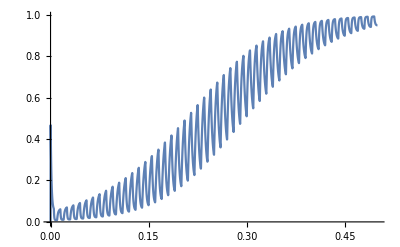

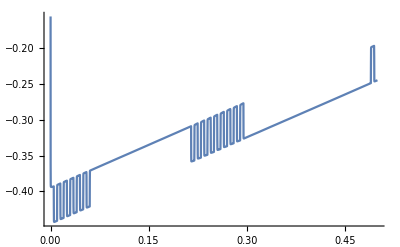

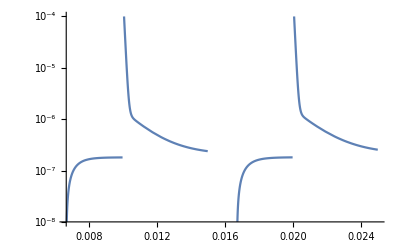

```mathematica
(*Define rate constants based on VAptamerGold*)
kox[t_]:=(1-fBound) k0u Exp[alpha F (VAptamerGold[t]-E0)/(R T)]+fBound k0b Exp[alpha F (VAptamerGold[t]-E0)/(R T)];

kred[t_]:=(1-fBound) k0u Exp[-(1-alpha) F (VAptamerGold[t]-E0)/(R T)]+fBound k0b Exp[-(1-alpha) F (VAptamerGold[t]-E0)/(R T)];

(*Oxidation fraction differential equation*)
aptamerODE=fOx'[t]==kox[t] (1-fOx[t])-kred[t] fOx[t];
initialAptamer=fOx[0]==0;


(* Circuit Equations *)

(*Current through capacitor*)
iCap[t_]:=Cint VAptamerGold'[t];

(*Current through aptamer*)
iAptamer[t_]:=nElec*F*A*Lambda*(kox[t]*(1-fOx[t])-kred[t]*fOx[t]);

(*Total current through resistor*)
iTotal[t_]:=iCap[t]+iAptamer[t];

(*Voltage drop across resistor*)
circuitODE=VApplied[t]-VAptamerGold[t]==RSol*iTotal[t];

VCap0 =0; (* assume initial charge zero *)

(*Initial voltage condition*)
initialRC=VAptamerGold[0]==VCap0;


(*Solve for VAptamerGold and fOx simultaneously*)
solution=NDSolve[{aptamerODE,circuitODE,initialAptamer,initialRC},{fOx,VAptamerGold},{t,0,Tmax}];

(*Redefine functions using solution*)
fOxSol[t_]:=fOx[t]/. solution[[1]];
VAptamerSol[t_]:=VAptamerGold[t]/. solution[[1]]

i[t_] :=(VApplied[t]-VAptamerGold[t]/. solution[[1]])/RSol;

Plot[fOxSol[t],{t,0,Tmax}]

(*Plot total current*)
Plot[{VAptamerSol[t]},{t,0,Tmax}, PlotRange->{Automatic, Automatic}]
LogPlot[{i[t]},{t,0,Tmax/20}, PlotRange->{Automatic, {10^-8, 10^-4}}]
```

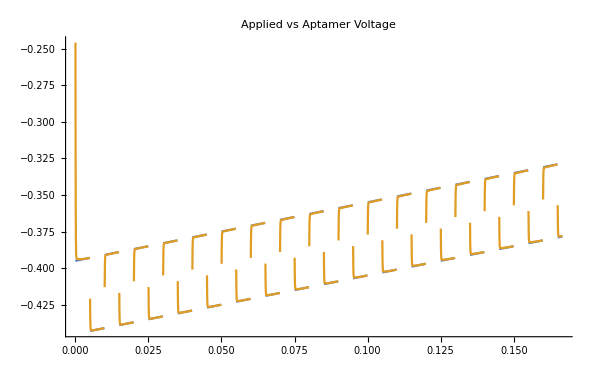

```mathematica
(*Visual Check*)
Plot[{VApplied[t],VAptamerSol[t]},{t,0,Tmax/3},PlotLabel->"Applied vs Aptamer Voltage"]
```

```mathematica
(*Noise Modeling*)

(*Generate noise values at sampled points*)
(* need to replace this with frequency-domain noise function later! *)
(*Compute Noisy Signal at Sampled Points*)
(*Generate noise values*)
noiseStd=1*10^-9; (*Standard deviation of noise in Amperes*)
noisyCurrent[t_] := i[t] + RandomReal[NormalDistribution[0,noiseStd]];

(*Evaluate model current and add noise*)
noisyCurrentSamples=Table[{timeSamples[[n]],noisyCurrent[timeSamples[[n]]]},{n,Length[timeSamples]}];
```

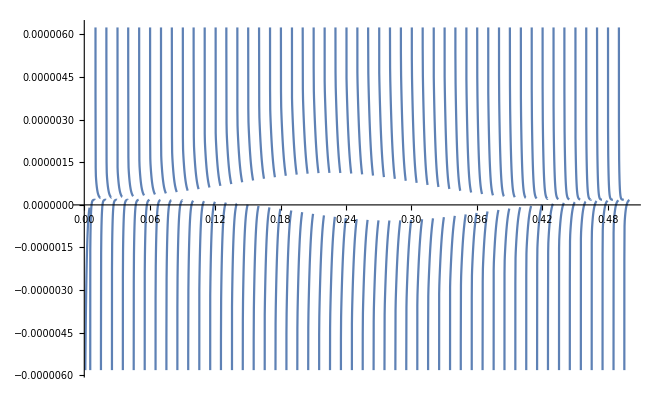

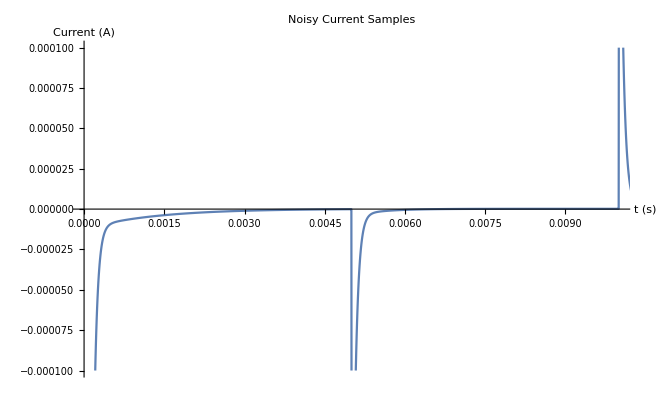

```mathematica
-Graphics-;
(* from Finding the lost dissociation constant of
electrochemical aptamer-based biosensors *) 


(* maybe we can use above, with an assumption about noise being thermal (proportional to Real R?? *)
(* let's take noise to be a power law function of frequency *)
(* we actually want just an aptamer measured for 12 hours with nothing happenening and then we take the PSD of that *)
(* has anyone measured that ?!?! *)

-Graphics-;
-Graphics-;
(* can we reproduce above? *) 
(* from Comparison of voltammetric methods used in the
interrogation of electrochemical aptamer-based
sensors *)
Plot[noisyCurrent[t],{t,0,Tmax}]
(*Plot noisy current*)
ListPlot[noisyCurrentSamples,PlotLabel->"Noisy Current Samples",AxesLabel->{"t (s)","Current (A)"},Joined->True, PlotRange->{{0,0.01},{-10^-4,1*10^-4}}]
```

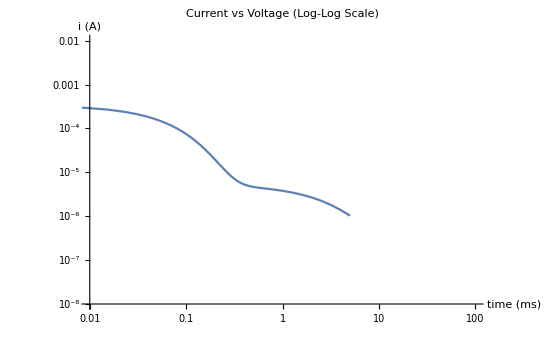

```mathematica
timeRange=Range[Tmax/2,Tmax/2+1/(2*squareWaveFreq),dt];

voltageTimePairs=Table[{(t-Tmax/2)*1000,noisyCurrent[t]},{t,timeRange}]; (* time in ms *)

(*Plot voltage vs current*)
ListLogLogPlot[voltageTimePairs,AxesLabel->{"time (ms)","i (A)"},PlotLabel->"Current vs Voltage (Log-Log Scale)", PlotRange -> {{0.01, 100}, {10^-8,10^-2}}, Joined-> True]
```

```mathematica
-Graphics-; (* from Arroyo-Currás et al.2018. Copyright 2018 American Chemical Society *)
```

```mathematica
(* Generate a list of SWV data points *)
(* iForwardSWV and iReverseSWV and IdiffSWV *)
(* First: get the time before each a potential switch in VAptamerGold[t] for forward steps and backward steps *)

(* Next: using the iForwardStepTimes list calculate the current at that time iForwardSWV[t] *) 
(* Next: using the iReverseStepTimes list calculate the current at that time iReverseSWV[t] *) 
(* Finally calculate idiffSWV as the difference between forward and reverse *)
```

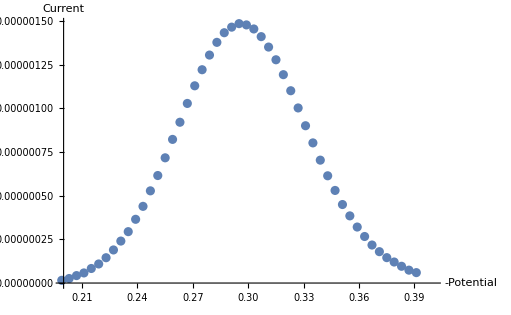

```mathematica
(*Compute Forward and Reverse Currents at Each Step*)

(*Example noisyCurrentSamples structure*)(*noisyCurrentSamples={{t1,i1},{t2,i2},{t3,i3},...,{tn,in}}*)(*For each switch time,find the nearest earlier time point*)(*Function to find the current value just before each switch time*)findPrecedingCurrent[switchTimes_List,data_List]:=Module[{times=data[[All,1]],result},result=Table[Block[{index},index=SelectFirst[Reverse[Range[Length[times]]],times[[#]]<t&,Missing["NotAvailable"]];
If[MissingQ[index],{t,Missing["NotAvailable"]},data[[index]]]],{t,switchTimes}];
result];
iSWVFWDExp=findPrecedingCurrent[downSwitchTimes,noisyCurrentSamples];
iSWVREVExp=findPrecedingCurrent[upSwitchTimes,noisyCurrentSamples];

(*Calculate difference *)
iSWVDiff=Table[{-VApplied[upSwitchTimes[[n]]],iSWVFWDExp[[n,2]]-iSWVREVExp[[n,2]]},{n,1,Min[Length[iSWVFWDExp],Length[iSWVREVExp]]}];iSWVFWDvsV=Table[{-VApplied[upSwitchTimes[[n]]],iSWVFWDExp[[n,2]]},{n,1,Min[Length[iSWVFWDExp],Length[iSWVREVExp]]}];
iSWVRRevVSV=Table[{-VApplied[upSwitchTimes[[n]]],iSWVREVExp[[n,2]]},{n,1,Min[Length[iSWVREVExp],Length[iSWVREVExp]]}];

ListPlot[noisyCurrentSamples];
ListPlot[{iSWVFWDvsV, iSWVRRevVSV, iSWVDiff}, AxesLabel->{"-Potential", "Current"}, PlotRange->{{0.2,0.4}, Automatic}];
ListPlot[{ iSWVDiff}, AxesLabel->{"-Potential", "Current"}, PlotRange->{{0.2,0.4}, Automatic}]

(* can we predict shape of amplitude vs potential from this?!? *)
(* figure S1 of Comparison of voltammetric methods used in the interrogation of
electrochemical aptamer-based sensors *)
-Graphics-;
```

```mathematica
(* get Square Wave results as a function of period *)
(* Now let's get KDM for 2 representative periods *)
-Graphics-;
```